# He_3 H^+

## Modules

Format the hamiltonian from qiskit; daniel’s format

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits},
stringham=Import[filename];
ham=ToExpression[stringham];
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]
```

## Hamiltonian generation

```mathematica
{hamiltonian,nterms,nqubits}=FormatHamiltonian["~/vqe/molecules/He3H/he3h.txt"];
```

```mathematica
{nqubits,nterms}
```

{8,193}

```mathematica
eigenvals=Eigenvalues@CalcPauliSumMatrix@hamiltonian;
```

```mathematica
groundstate=Min@eigenvals
```

-8.57531

```mathematica
conf=DefaultConfig@nqubits
```

<|nqubit→8,methode→NG,gatespercycle→20,ngatesinit→40,fixansatz→{},fixansatzparams→<||>,ansatzspace→{0,1,2,3,4,5,6,7},weightgate→{1→0.3,2→0.7},ansatzinit→{X_0,X_1,X_2,X_3,X_4,X_5,X_6},swapfabricdepth→0,maxfevbf→100,greediness→8,greedinessinit→8,greedflat→0.01,maxgreediter→100,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/1000,θignore→1/1000,metignore→1/1000,perfectingflat→0.00015,pruningerror→0.1,iterconverge→20,globalconverge→2,θinitrange→π/4,ϵfin→1/10000000,slowfirst→True,refine→2,gateset→{Rx_#1[θ]&,Ry_#1[θ]&,Rz_#1[θ]&,C_#1[Rx_#2[θ]]&,C_#1[Ry_#2[θ]]&,C_#1[Rz_#2[θ]]&}|>

## The runs

Trial 1

Tue 8 Feb 2022 11:00:55GMT

target: -8.57531

@cycle1, fev:925, <E>: -8.57531363253082 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 21, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:1069, <E>: -8.57531363253082 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 21, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:1417, <E>: -8.57531363253082 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 21, 0}

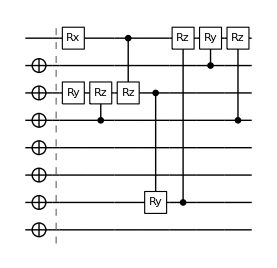

runtime=0.0754041 hours

nansatz=8

nansatz/cycle={0,8,8}

<E>/cycle={-8.56935,-8.57531,-8.57531}

ϵ/cycle={0.00596031,1.08709×10^-6,1.08709×10^-6}

<E>=-8.57531

<E>-E_gs=1.08709×10^-6

Trial 2

Tue 8 Feb 2022 11:05:26GMT

target: -8.57531

@cycle1, fev:637, <E>: -8.575312888292697 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 9, 10, 16, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:762, <E>: -8.575312888292697 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 9, 10, 16, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:1011, <E>: -8.575312888292697 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 9, 10, 16, 0}

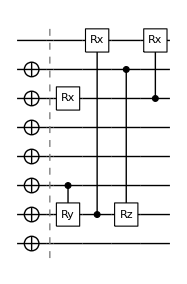

runtime=0.0547159 hours

nansatz=5

nansatz/cycle={0,5,5}

<E>/cycle={-8.56935,-8.57531,-8.57531}

ϵ/cycle={0.00596031,1.83132×10^-6,1.83132×10^-6}

<E>=-8.57531

<E>-E_gs=1.83132×10^-6

Trial 3

Tue 8 Feb 2022 11:08:43GMT

target: -8.57531

@cycle1, fev:550, <E>: -8.575272940616106 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 25, 1}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:660, <E>: -8.575272940616106 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 25, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:844, <E>: -8.575272940616106 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 25, 0}

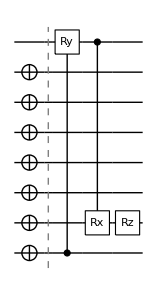

runtime=0.0462156 hours

nansatz=3

nansatz/cycle={0,3,3}

<E>/cycle={-8.56935,-8.57527,-8.57527}

ϵ/cycle={0.00596031,0.000041779,0.000041779}

<E>=-8.57527

<E>-E_gs=0.000041779

Trial 4

Tue 8 Feb 2022 11:11:30GMT

target: -8.57531

@cycle1, fev:900, <E>: -8.57530745944021 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 6, 5, 20, 1}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:1067, <E>: -8.57530745944021 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 6, 5, 20, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:1533, <E>: -8.57530745944021 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 6, 5, 20, 0}

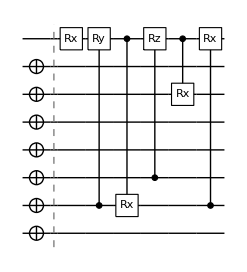

runtime=0.0824648 hours

nansatz=6

nansatz/cycle={0,6,6}

<E>/cycle={-8.56935,-8.57531,-8.57531}

ϵ/cycle={0.00596031,7.26018×10^-6,7.26018×10^-6}

<E>=-8.57531

<E>-E_gs=7.26018×10^-6

Trial 5

Tue 8 Feb 2022 11:16:27GMT

target: -8.57531

@cycle1, fev:705, <E>: -8.575312287238805 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 10, 9, 11, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:883, <E>: -8.575312287238805 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 10, 9, 11, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:1285, <E>: -8.575312287238805 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 10, 9, 11, 0}

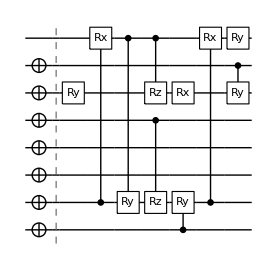

runtime=0.072448 hours

nansatz=10

nansatz/cycle={0,10,10}

<E>/cycle={-8.56935,-8.57531,-8.57531}

ϵ/cycle={0.00596031,2.43238×10^-6,2.43238×10^-6}

<E>=-8.57531

<E>-E_gs=2.43238×10^-6

Trial 6

Tue 8 Feb 2022 11:20:47GMT

target: -8.57531

@cycle1, fev:668, <E>: -8.575303136974487 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 20, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:972, <E>: -8.575303136974487 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 20, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:1452, <E>: -8.575303136974487 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 20, 0}

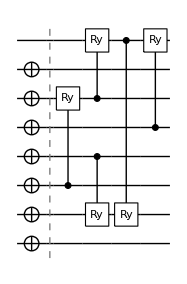

runtime=0.0729361 hours

nansatz=5

nansatz/cycle={0,5,5}

<E>/cycle={-8.56935,-8.5753,-8.5753}

ϵ/cycle={0.00596031,0.0000115826,0.0000111235}

<E>=-8.5753

<E>-E_gs=0.0000111235

Trial 7

Tue 8 Feb 2022 11:25:10GMT

target: -8.57531

@cycle1, fev:1076, <E>: -8.575314314418042 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 22, 1}

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:1266, <E>: -8.575314314418042 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 22, 0}

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:1567, <E>: -8.575314314418042 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 22, 2}

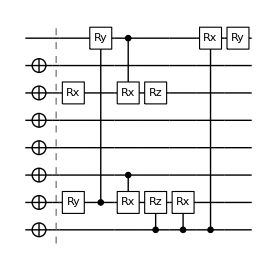

runtime=0.0900231 hours

nansatz=10

nansatz/cycle={0,10,10}

<E>/cycle={-8.56935,-8.57531,-8.57531}

ϵ/cycle={0.00596031,4.05198×10^-7,4.05198×10^-7}

<E>=-8.57531

<E>-E_gs=4.05198×10^-7

Trial 8

Tue 8 Feb 2022 11:30:34GMT

target: -8.57531

@cycle1, fev:763, <E>: -8.575312958604188 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 7, 9, 14, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:894, <E>: -8.575312958604188 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 7, 9, 14, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:1229, <E>: -8.575312958604188 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 7, 9, 14, 0}

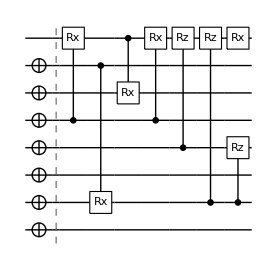

runtime=0.069709 hours

nansatz=8

nansatz/cycle={0,8,8}

<E>/cycle={-8.56935,-8.57531,-8.57531}

ϵ/cycle={0.00596031,1.76101×10^-6,1.76101×10^-6}

<E>=-8.57531

<E>-E_gs=1.76101×10^-6

Trial 9

Tue 8 Feb 2022 11:34:45GMT

target: -8.57531

@cycle1, fev:472, <E>: -8.575273017646332 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 13, 14, 7, 0}

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:633, <E>: -8.575273017646332 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 13, 14, 7, 0}

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:815, <E>: -8.575273017646332 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 13, 14, 7, 0}

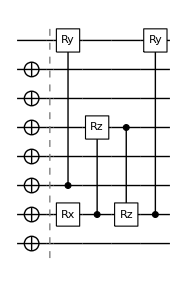

runtime=0.0469098 hours

nansatz=5

nansatz/cycle={0,5,5}

<E>/cycle={-8.56935,-8.57527,-8.57527}

ϵ/cycle={0.00596031,0.000041702,0.000041702}

<E>=-8.57527

<E>-E_gs=0.000041702

Trial 10

Tue 8 Feb 2022 11:37:34GMT

target: -8.57531

@cycle1, fev:796, <E>: -8.575310813280382 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 14, 7, 13, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:911, <E>: -8.575310813280382 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 14, 7, 13, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:1283, <E>: -8.575310813280382 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 14, 7, 13, 0}

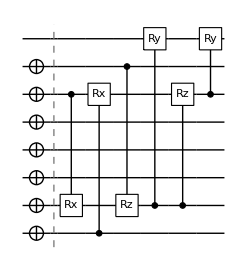

runtime=0.0682255 hours

nansatz=6

nansatz/cycle={0,6,6}

<E>/cycle={-8.56935,-8.57531,-8.57531}

ϵ/cycle={0.00596031,3.90634×10^-6,3.90634×10^-6}

<E>=-8.57531

<E>-E_gs=3.90634×10^-6

{-8.57531,-8.57531,-8.57527,-8.57531,-8.57531,-8.5753,-8.57531,-8.57531,-8.57527,-8.57531}

```mathematica
results={};
Table[
Print["Trial ",trial];
Print@Now;
Print["target: ",groundstate];
DestroyAllQuregs[];
conf=DefaultConfig[nqubits];
{timing,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elim}}=AbsoluteTiming[VQEGS[nqubits,hamiltonian,conf]];

Print@DrawCircuit[{conf["ansatzinit"],ansatz},nqubits];
Print["runtime=",timing/3600," hours"];
Print["nansatz=",Length@ansatz];
Print["nansatz/cycle=",Length@#&/@cycleres["ansatz"]];
Print["<E>/cycle=",cycleres["E"]];
Print["ϵ/cycle=",cycleres["E"]-groundstate];
{ψ,ψwork}=CreateQuregs[nqubits,2];
ApplyCircuit[ψ,Join[conf["ansatzinit"],ansatz]/.θvars];
ecur=CalcExpecPauliSum[ψ,hamiltonian,ψwork];
Print["<E>=",ecur];
Print["<E>-E_gs=",ecur-groundstate];
DestroyAllQuregs[];
AppendTo[results,{ansatz,θvars,timing,cycleres,fev,aborted,elim}];
ecur
,{trial,10}]
```

## Total results

```mathematica
{ψ,ψwork}=CreateQuregs[nqubits,2];
ansatzinit=Table[Subscript[X, j],{j,0,6}];
chemacc=1.59*10^-3;
trial=1;
disp1=Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
{trial++,
res⟦3⟧/60,
ϵgs<chemacc,
ϵgs,
Length@res⟦1⟧,
ToString[res⟦-1⟧],
ToString[res⟦-3⟧],
ToString[Length[#]&/@res⟦4⟧⟦"ansatz"⟧],
ToString[res⟦-2⟧]
}
,{res,results}];
PrependTo[disp1,{"trial","runtime(min)","chemacc?","ϵgs","ngates", "elims","fevs","ngates/pcycle","aborted cycle"}];
DestroyAllQuregs[]
```

```mathematica
disp1//TableForm
```

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/pcycle | aborted cycle
1 | 4.52424 | True | 1.08709×10^-6 | 8 | {0, 11, 0, 21} | 1520 | {0, 8, 8} | {}
2 | 3.28296 | True | 1.83132×10^-6 | 5 | {0, 9, 10, 16} | 1081 | {0, 5, 5} | {}
3 | 2.77294 | True | 0.000041779 | 3 | {0, 11, 0, 25} | 897 | {0, 3, 3} | {}
4 | 4.94789 | True | 7.26018×10^-6 | 6 | {2, 6, 5, 20} | 1657 | {0, 6, 6} | {}
5 | 4.34688 | True | 2.43238×10^-6 | 10 | {0, 10, 9, 11} | 1460 | {0, 10, 10} | {}
6 | 4.37616 | True | 0.0000111235 | 5 | {0, 15, 0, 20} | 1555 | {0, 5, 5} | {}
7 | 5.40138 | True | 4.05198×10^-7 | 10 | {0, 8, 0, 22} | 1785 | {0, 10, 10} | {2, 3}
8 | 4.18254 | True | 1.76101×10^-6 | 8 | {0, 7, 9, 14} | 1351 | {0, 8, 8} | {}
9 | 2.81459 | True | 0.000041702 | 5 | {1, 13, 14, 7} | 919 | {0, 5, 5} | {2, 3}
10 | 4.09353 | True | 3.90634×10^-6 | 6 | {0, 14, 7, 13} | 1422 | {0, 6, 6} | {}

```mathematica
results
```

{{{Ry_5[θ_1],Rx_7[θ_27],C_4[Rz_5[θ_21]],C_7[Rz_5[θ_31]],C_5[Ry_1[θ_13]],C_1[Rz_7[θ_3]],C_6[Ry_7[θ_26]],C_4[Rz_7[θ_22]]},<|θ_1→-0.0117319,θ_3→3.13502,θ_13→0.144507,θ_21→1.4133,θ_22→-1.57152,θ_26→-1.5708,θ_27→1.5708,θ_31→-3.12846|>,271.455,<|ansatz→{{},{Ry_5[θ_1],Rx_7[θ_27],C_4[Rz_5[θ_21]],C_7[Rz_5[θ_31]],C_5[Ry_1[θ_13]],C_1[Rz_7[θ_3]],C_6[Ry_7[θ_26]],C_4[Rz_7[θ_22]]},{Ry_5[θ_1],Rx_7[θ_27],C_4[Rz_5[θ_21]],C_7[Rz_5[θ_31]],C_5[Ry_1[θ_13]],C_1[Rz_7[θ_3]],C_6[Ry_7[θ_26]],C_4[Rz_7[θ_22]]}},θvars→{<||>,<|θ_1→-0.0117319,θ_3→3.13502,θ_13→0.144507,θ_21→1.4133,θ_22→-1.57152,θ_26→-1.5708,θ_27→1.5708,θ_31→-3.12846|>,<|θ_1→-0.0117319,θ_3→3.13502,θ_13→0.144507,θ_21→1.4133,θ_22→-1.57152,θ_26→-1.5708,θ_27→1.5708,θ_31→-3.12846|>},E→{-8.56935,-8.57531,-8.57531},idx→{1,41,41}|>,1520,{},{0,11,0,21}},{{C_2[Ry_1[θ_18]],Rx_5[θ_6],C_1[Rx_7[θ_2]],C_6[Rz_1[θ_37]],C_5[Rx_7[θ_30]]},<|θ_2→-3.14052,θ_6→0.0111805,θ_18→0.144636,θ_30→3.14053,θ_37→1.55495|>,196.977,<|ansatz→{{},{C_2[Ry_1[θ_18]],Rx_5[θ_6],C_1[Rx_7[θ_2]],C_6[Rz_1[θ_37]],C_5[Rx_7[θ_30]]},{C_2[Ry_1[θ_18]],Rx_5[θ_6],C_1[Rx_7[θ_2]],C_6[Rz_1[θ_37]],C_5[Rx_7[θ_30]]}},θvars→{<||>,<|θ_2→-3.14052,θ_6→0.0111805,θ_18→0.144636,θ_30→3.14053,θ_37→1.55495|>,<|θ_2→-3.14052,θ_6→0.0111805,θ_18→0.144636,θ_30→3.14053,θ_37→1.55495|>},E→{-8.56935,-8.57531,-8.57531},idx→{1,41,41}|>,1081,{},{0,9,10,16}},{{C_0[Ry_7[θ_28]],C_7[Rx_1[θ_9]],Rz_1[θ_6]},<|θ_6→1.57321,θ_9→3.14683,θ_28→-0.144889|>,166.376,<|ansatz→{{},{C_0[Ry_7[θ_28]],C_7[Rx_1[θ_9]],Rz_1[θ_6]},{C_0[Ry_7[θ_28]],C_7[Rx_1[θ_9]],Rz_1[θ_6]}},θvars→{<||>,<|θ_6→1.57321,θ_9→3.14683,θ_28→-0.144889|>,<|θ_6→1.57321,θ_9→3.14683,θ_28→-0.144889|>},E→{-8.56935,-8.57527,-8.57527},idx→{1,41,41}|>,897,{},{0,11,0,25}},{{Rx_7[θ_4],C_1[Ry_7[θ_29]],C_7[Rx_1[θ_26]],C_2[Rz_7[θ_20]],C_7[Rx_5[θ_21]],C_1[Rx_7[θ_39]]},<|θ_4→-0.335492,θ_20→0.792446,θ_21→0.0440039,θ_26→0.608134,θ_29→0.36079,θ_39→0.466404|>,296.873,<|ansatz→{{},{Rx_7[θ_4],C_1[Ry_7[θ_29]],C_7[Rx_1[θ_26]],C_2[Rz_7[θ_20]],C_7[Rx_5[θ_21]],C_1[Rx_7[θ_39]]},{Rx_7[θ_4],C_1[Ry_7[θ_29]],C_7[Rx_1[θ_26]],C_2[Rz_7[θ_20]],C_7[Rx_5[θ_21]],C_1[Rx_7[θ_39]]}},θvars→{<||>,<|θ_4→-0.335492,θ_20→0.792446,θ_21→0.0440039,θ_26→0.608134,θ_29→0.36079,θ_39→0.466404|>,<|θ_4→-0.335492,θ_20→0.792446,θ_21→0.0440039,θ_26→0.608134,θ_29→0.36079,θ_39→0.466404|>},E→{-8.56935,-8.57531,-8.57531},idx→{1,41,41}|>,1657,{},{2,6,5,20}},{{Ry_5[θ_26],C_1[Rx_7[θ_31]],C_7[Ry_1[θ_39]],C_4[Rz_1[θ_1]],C_7[Rz_5[θ_4]],C_0[Ry_1[θ_22]],Rx_5[θ_17],C_1[Rx_7[θ_14]],C_6[Ry_5[θ_18]],Ry_7[θ_9]},<|θ_1→1.68242,θ_4→0.228036,θ_9→-0.0728106,θ_14→-0.693686,θ_17→0.00426811,θ_18→-0.144393,θ_22→0.00596346,θ_26→0.144914,θ_31→0.710994,θ_39→0.418585|>,260.813,<|ansatz→{{},{Ry_5[θ_26],C_1[Rx_7[θ_31]],C_7[Ry_1[θ_39]],C_4[Rz_1[θ_1]],C_7[Rz_5[θ_4]],C_0[Ry_1[θ_22]],Rx_5[θ_17],C_1[Rx_7[θ_14]],C_6[Ry_5[θ_18]],Ry_7[θ_9]},{Ry_5[θ_26],C_1[Rx_7[θ_31]],C_7[Ry_1[θ_39]],C_4[Rz_1[θ_1]],C_7[Rz_5[θ_4]],C_0[Ry_1[θ_22]],Rx_5[θ_17],C_1[Rx_7[θ_14]],C_6[Ry_5[θ_18]],Ry_7[θ_9]}},θvars→{<||>,<|θ_1→1.68242,θ_4→0.228036,θ_9→-0.0728106,θ_14→-0.693686,θ_17→0.00426811,θ_18→-0.144393,θ_22→0.00596346,θ_26→0.144914,θ_31→0.710994,θ_39→0.418585|>,<|θ_1→1.68242,θ_4→0.228036,θ_9→-0.0728106,θ_14→-0.693686,θ_17→0.00426811,θ_18→-0.144393,θ_22→0.00596346,θ_26→0.144914,θ_31→0.710994,θ_39→0.418585|>},E→{-8.56935,-8.57531,-8.57531},idx→{1,41,41}|>,1460,{},{0,10,9,11}},{{C_2[Ry_5[θ_20]],C_3[Ry_1[θ_25]],C_5[Ry_7[θ_36]],C_7[Ry_1[θ_39]],C_4[Ry_7[θ_40]]},<|θ_20→-0.00910138,θ_25→-0.211324,θ_36→-1.94279,θ_39→0.309539,θ_40→1.9469|>,262.57,<|ansatz→{{},{C_2[Ry_5[θ_20]],C_3[Ry_1[θ_25]],C_5[Ry_7[θ_36]],C_7[Ry_1[θ_39]],C_4[Ry_7[θ_40]]},{C_2[Ry_5[θ_20]],C_3[Ry_1[θ_25]],C_5[Ry_7[θ_36]],C_7[Ry_1[θ_39]],C_4[Ry_7[θ_40]]}},θvars→{<||>,<|θ_20→-0.00924139,θ_25→-0.202687,θ_36→-1.90364,θ_39→0.305154,θ_40→1.90728|>,<|θ_20→-0.00910138,θ_25→-0.211324,θ_36→-1.94279,θ_39→0.309539,θ_40→1.9469|>},E→{-8.56935,-8.5753,-8.5753},idx→{1,41,41}|>,1555,{},{0,15,0,20}},{{Ry_1[θ_1],Rx_5[θ_30],C_1[Ry_7[θ_5]],C_2[Rx_1[θ_10]],C_7[Rx_5[θ_32]],C_0[Rz_1[θ_24]],Rz_5[θ_37],C_0[Rx_1[θ_27]],C_0[Rx_7[θ_35]],Ry_7[θ_38]},<|θ_1→-0.203832,θ_5→-1.58138,θ_10→-0.305842,θ_24→-0.449651,θ_27→0.337036,θ_30→-0.0112388,θ_32→0.0224961,θ_35→0.42587,θ_37→1.11856,θ_38→1.57067|>,324.083,<|ansatz→{{},{Ry_1[θ_1],Rx_5[θ_30],C_1[Ry_7[θ_5]],C_2[Rx_1[θ_10]],C_7[Rx_5[θ_32]],C_0[Rz_1[θ_24]],Rz_5[θ_37],C_0[Rx_1[θ_27]],C_0[Rx_7[θ_35]],Ry_7[θ_38]},{Ry_1[θ_1],Rx_5[θ_30],C_1[Ry_7[θ_5]],C_2[Rx_1[θ_10]],C_7[Rx_5[θ_32]],C_0[Rz_1[θ_24]],Rz_5[θ_37],C_0[Rx_1[θ_27]],C_0[Rx_7[θ_35]],Ry_7[θ_38]}},θvars→{<||>,<|θ_1→-0.203832,θ_5→-1.58138,θ_10→-0.305842,θ_24→-0.449651,θ_27→0.337036,θ_30→-0.0112388,θ_32→0.0224961,θ_35→0.42587,θ_37→1.11856,θ_38→1.57067|>,<|θ_1→-0.203832,θ_5→-1.58138,θ_10→-0.305842,θ_24→-0.449651,θ_27→0.337036,θ_30→-0.0112388,θ_32→0.0224961,θ_35→0.42587,θ_37→1.11856,θ_38→1.57067|>},E→{-8.56935,-8.57531,-8.57531},idx→{1,41,41}|>,1785,{2,3},{0,8,0,22}},{{C_4[Rx_7[θ_26]],C_6[Rx_1[θ_17]],C_7[Rx_5[θ_11]],C_4[Rx_7[θ_30]],C_3[Rz_7[θ_34]],C_1[Rz_7[θ_23]],Rx_7[θ_5],C_1[Rz_3[θ_22]]},<|θ_5→1.5713,θ_11→-0.272784,θ_17→0.142587,θ_22→3.1416,θ_23→-3.14393,θ_26→0.0810989,θ_30→-1.65164,θ_34→3.14543|>,250.953,<|ansatz→{{},{C_4[Rx_7[θ_26]],C_6[Rx_1[θ_17]],C_7[Rx_5[θ_11]],C_4[Rx_7[θ_30]],C_3[Rz_7[θ_34]],C_1[Rz_7[θ_23]],Rx_7[θ_5],C_1[Rz_3[θ_22]]},{C_4[Rx_7[θ_26]],C_6[Rx_1[θ_17]],C_7[Rx_5[θ_11]],C_4[Rx_7[θ_30]],C_3[Rz_7[θ_34]],C_1[Rz_7[θ_23]],Rx_7[θ_5],C_1[Rz_3[θ_22]]}},θvars→{<||>,<|θ_5→1.5713,θ_11→-0.272784,θ_17→0.142587,θ_22→3.1416,θ_23→-3.14393,θ_26→0.0810989,θ_30→-1.65164,θ_34→3.14543|>,<|θ_5→1.5713,θ_11→-0.272784,θ_17→0.142587,θ_22→3.1416,θ_23→-3.14393,θ_26→0.0810989,θ_30→-1.65164,θ_34→3.14543|>},E→{-8.56935,-8.57531,-8.57531},idx→{1,41,41}|>,1351,{},{0,7,9,14}},{{Rx_1[θ_12],C_2[Ry_7[θ_24]],C_1[Rz_4[θ_16]],C_4[Rz_1[θ_26]],C_1[Ry_7[θ_38]]},<|θ_12→-0.144624,θ_16→1.15158,θ_24→-3.14159,θ_26→-2.14685,θ_38→3.14159|>,168.875,<|ansatz→{{},{Rx_1[θ_12],C_2[Ry_7[θ_24]],C_1[Rz_4[θ_16]],C_4[Rz_1[θ_26]],C_1[Ry_7[θ_38]]},{Rx_1[θ_12],C_2[Ry_7[θ_24]],C_1[Rz_4[θ_16]],C_4[Rz_1[θ_26]],C_1[Ry_7[θ_38]]}},θvars→{<||>,<|θ_12→-0.144624,θ_16→1.15158,θ_24→-3.14159,θ_26→-2.14685,θ_38→3.14159|>,<|θ_12→-0.144624,θ_16→1.15158,θ_24→-3.14159,θ_26→-2.14685,θ_38→3.14159|>},E→{-8.56935,-8.57527,-8.57527},idx→{1,41,41}|>,919,{2,3},{1,13,14,7}},{{C_5[Rx_1[θ_4]],C_0[Rx_5[θ_15]],C_6[Rz_1[θ_21]],C_1[Ry_7[θ_23]],C_1[Rz_5[θ_24]],C_5[Ry_7[θ_32]]},<|θ_4→-0.144893,θ_15→0.0108313,θ_21→-0.927816,θ_23→3.13941,θ_24→-1.27915,θ_32→-3.1394|>,245.612,<|ansatz→{{},{C_5[Rx_1[θ_4]],C_0[Rx_5[θ_15]],C_6[Rz_1[θ_21]],C_1[Ry_7[θ_23]],C_1[Rz_5[θ_24]],C_5[Ry_7[θ_32]]},{C_5[Rx_1[θ_4]],C_0[Rx_5[θ_15]],C_6[Rz_1[θ_21]],C_1[Ry_7[θ_23]],C_1[Rz_5[θ_24]],C_5[Ry_7[θ_32]]}},θvars→{<||>,<|θ_4→-0.144893,θ_15→0.0108313,θ_21→-0.927816,θ_23→3.13941,θ_24→-1.27915,θ_32→-3.1394|>,<|θ_4→-0.144893,θ_15→0.0108313,θ_21→-0.927816,θ_23→3.13941,θ_24→-1.27915,θ_32→-3.1394|>},E→{-8.56935,-8.57531,-8.57531},idx→{1,41,41}|>,1422,{},{0,14,7,13}}}